```mathematica
(* This program solves for a high pass filter network as described in the Knoll Textbook *)
```

```mathematica
D[Sin[2 Pi f t],t]
```

2 f π Cos[2 f π t]

```mathematica
Vin[f_,Vo_,t_]:=Vo Sin[2 Pi f t]
```

```mathematica
DSolve[{Vo 2 Pi f*Cos[2 Pi f t]==V[t]/tau+V'[t],V[0]==0},V[t],t]
```

{{V[t]→(2 ⅇ^(-t/tau) f π tau Vo (-1+ⅇ^(t/tau) Cos[2 f π t]+2 ⅇ^(t/tau) f π tau Sin[2 f π t]))/(1+4 f^2 π^2 tau^2)}}

```mathematica
V[tau_,f_,Vo_,t_]:=(2 ⅇ^(-t/tau) f π tau Vo (-1+ⅇ^(t/tau) Cos[2 f π t]+2 ⅇ^(t/tau) f π tau Sin[2 f π t]))/(1+4 f^2 π^2 tau^2)
```

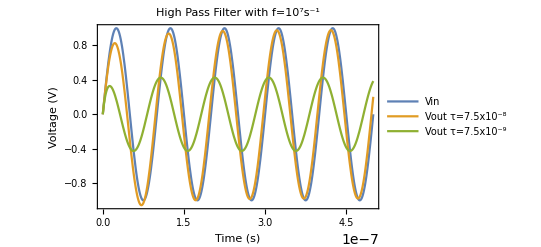

```mathematica
Plot[{Vin[10^7,1,t],V[0.075*10^-6,10^7,1,t],V[0.0075*10^-6,10^7,1,t]},{t,0,0.5*10^-6},FrameTicksStyle->Directive[Black],PlotLabel->Style["High Pass Filter with f=10^7s^-1",Black,16], Frame->True,FrameLabel->{Style["Time (s)",Black,16],Style["Voltage (V)",Black,16]},PlotLegends->{"Vin","Vout τ=7.5x10^-8","Vout τ=7.5x10^-9"},PlotRange->All]
```